```mathematica
FullSimplify[3*Sum[LegendreP[2*n,F]/((2*n+1)*(2*n+3))*(c1/R)^(2*n),{n,0,2}]]
```

1+(3 c1^4 (3-30 F^2+35 F^4))/(280 R^4)+(c1^2 (-1+3 F^2))/(10 R^2)

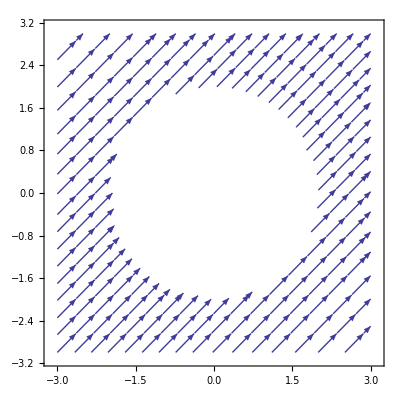

```mathematica
(*<<VectorAnalysis`
SetCoordinates[Spherical]
exp = Grad[FullSimplify[3*Sum[LegendreP[2*n,Cos[Pphi]]/((2*n+1)*(2*n+3))*(c1/Rr)^(2*n),{n,0,1}]/Rr]]
VectorDensityPlot[{-(1/Rr^2+3*(Cos[Pphi]^3-1)/(10*Rr^4)),-3*Sin[Pphi]*Cos[Pphi]^2/(10*Rr^4)},{Rr,1,1.5},{Pphi,0,2*Pi}]*)
a=2;
b=2;
c1=Sqrt[a^2-b^2];
PolarStreamPlot[{rfield_,thetafield_},opts___]:=Module[{tocartesian,cartesianlist,field,cartesianfield},tocartesian={Overscript[r,_]->x/r Overscript[x,_]+y/r Overscript[y,_],Overscript[θ,_]->-(y/Sqrt[x^2+y^2])Overscript[x,_]+x/Sqrt[x^2+y^2] Overscript[y,_],r->Sqrt[x^2+y^2],θ->ArcTan[x,y]};
cartesianlist=(a_ Overscript[x,_]+b_ Overscript[y,_])->{a,b};
field=rfield Overscript[r,_]+thetafield Overscript[θ,_];
cartesianfield=FullSimplify[field//.tocartesian]/.cartesianlist;
StreamPlot[cartesianfield,opts]]
PolarStreamPlot[{-(1/r^2+3*(3*c1^2(Cos[θ]^3-1))/(10*r^4)) Overscript[r,_],-(3*c1^2*Sin[θ]*Cos[θ])/(10*r^4)}Overscript[θ,_],{x,-3,3},{y,-3,3},RegionFunction->Function[{x,y},x^2/a^2+y^2/b^2>1]]
```